```mathematica
ClearAll["Global`*"]
```

```mathematica
ass={r>0,z'[r]^2>0,CC>0}
```

{r>0,z'[r]^2>0,CC>0}

```mathematica
(*canoincal base vectors*)
```

```mathematica
ϵ[1]={1,0};
ϵ[2]={0,1};
```

```mathematica
g[r_]:={{1+(z'[r])^2,0},{0,r^2}}
```

```mathematica
detg[r_]:=Det[g[r]]
```

```mathematica
sqrtdetg[r_]:=Sqrt[detg[r]]
```

```mathematica
ig[r_]:=Inverse[g[r]]//FullSimplify
```

```mathematica
ig[r]
```

{{1/(1+z'[r]^2),0},{0,1/r^2}}

```mathematica
e[1][x_]:={Cos[x[[2]]], Sin[x[[2]]],z'[x[[1]]]} 
e[2][x_]:= {-x[[1]]Sin[x[[2]]],x[[1]] Cos[x[[2]]],0}
```

```mathematica
normal[x_]:=FullSimplify[Cross[e[1][x],e[2][x]]/sqrtdetg[x[[1]]],Assumptions->ass]
```

```mathematica
N3d[x_]:={-Cos[x[[2]]],-Sin[x[[2]]],0}
```

```mathematica
Clear[normNt]
```

```mathematica
Nt[r_]:=FullSimplify[Table[Sum[ig[r][[i,j]](N3d[{r,θ}].e[j][{r,θ}]),{j,1,2}],{i,1,2}],Assumptions->ass]
```

```mathematica
(*norm of Nt with respect to g*)
```

```mathematica
normNt[r_]:= Sqrt[Sum[Nt[r][[i]] Nt[r][[j]]*g[r][[i,j]],{i,1,2},{j,1,2}]]
```

```mathematica
Nt[r]/normNt[r]
```

{-√(1/(1+z'[r]^2)),0}

```mathematica
(*n^i at \partial \Omega_r*)
```

```mathematica
nRmin[x_]:=FullSimplify[{-x[[1]]/sqrtdetg[x[[1]]],0},Assumptions->ass]
```

```mathematica
(*n^i at \partial \Omega_R*)
```

```mathematica
nRmax[x_]:=FullSimplify[{x[[1]]/sqrtdetg[x[[1]]],0},Assumptions->ass]
```

```mathematica
(*normal to a curve γ given by a circle centered ar r=0*)
N3dγ[x_]:={Cos[x[[2]]], Sin[x[[2]]],0}
Ntγ[x_]:=Table[Sum[ig[x[[1]]][[i, j]] N3dγ[x].e[j][x],{j,1,2}],{i,1,2}]
nγ[x_]:=Ntγ[x]/Sqrt[Sum[Ntγ[x][[i]] Ntγ[x][[j]] *g[x[[1]]][[i,j]],{i,1,2},{j,1,2}]]//FullSimplify
```

```mathematica
(*omegaRmin(max)_here = omega_r(R)_const{variational_problem_bc_ring.py}*)
```

```mathematica
omegaRmin=nRmin[{Rmin,θ}].{z'[Rmin],0}
```

-(Rmin z'[Rmin])/(√(Rmin^2 (1+z'[Rmin]^2)))

```mathematica
omegaRmax=nRmax[{Rmax,θ}].{z'[Rmax],0}
```

(Rmax z'[Rmax])/(√(Rmax^2 (1+z'[Rmax]^2)))

```mathematica
(*second fundamental form b*)
```

```mathematica
Derivative[ϵ[1]][e[1]][{r,θ}].normal[{r,θ}]//FullSimplify
```

z''[r]/(√(1+z'[r]^2))

```mathematica
Derivative[ϵ[1]][e[2]][{r,θ}].normal[{r,θ}]//FullSimplify
```

0

```mathematica
Derivative[ϵ[2]][e[1]][{r,θ}].normal[{r,θ}]//FullSimplify
```

0

```mathematica
Derivative[ϵ[2]][e[2]][{r,θ}].normal[{r,θ}]//FullSimplify
```

(r z'[r])/(√(1+z'[r]^2))

```mathematica
b[r_]:={{Derivative[ϵ[1]][e[1]][{r,θ}].normal[{r,θ}],Derivative[ϵ[1]][e[2]][{r,θ}].normal[{r,θ}]},{Derivative[ϵ[2]][e[1]][{r,θ}].normal[{r,θ}],Derivative[ϵ[2]][e[2]][{r,θ}].normal[{r,θ}]}}//FullSimplify
```

```mathematica
H[r_]:=1/2 Tr[ig[r].b[r]]//FullSimplify
```

```mathematica
K[r_]:=Det[b[r]]/detg[r]//FullSimplify
```

```mathematica
(*momentum-flux tensor involving only the contribution from σ*)
```

```mathematica
Πσ[r_]:=Table[Table[-σ[r]ig[r][[i,j]],{j,1,2}],{i,1,2}]
```

```mathematica
(*force per unit length due to surface tension exerted on the curve γ (circle centered at r=0) with normal nγ *)
```

```mathematica
dFdlσt[r_]:=Table[Sum[Πσ[r][[i,j]] g[r][[j, k]]*nγ[{r,θ}][[k]],{j,1,2},{k,1,2}],{i,1,2}]
```

```mathematica
(*tangent force per unit length due to κ exerted on the curve γ (circle centered at r=0) with normal nγ *)
```

```mathematica
dFdlκt[r_]:=Table[-2 κ H[r]^2 nγ[{r,θ}][[i]],{i,1,2}]
```

```mathematica
(*normal force per unit length due to κ exerted on the curve γ (circle centered at r=0) with normal nγ *)
```

```mathematica
dFdlκn[r_]:=2 κ H'[r] nγ[{r,θ}][[1]]
```

```mathematica
(*tangent force per unit length, in the 3d space, due to σ, exerted on the curve γ (circle centered at r=0) with normal nγ *)
```

```mathematica
dFdlσ3d[r_,θ_]:=Sum[dFdlσt[r][[i]]e[i][{r,θ}],{i,1,2}]
```

```mathematica
(*tangent force per unit length, in the 3d space, due to κ exerted on the curve γ (circle centered at r=0) with normal nγ *)
```

```mathematica
dFdlκ3d[r_,θ_]:=Sum[dFdlκt[r][[i]]e[i][{r,θ}],{i,1,2}] +dFdlκn[r] normal[{r,θ}]
```

```mathematica
dFdlσκ3d[r_,θ_]:=dFdlσ3d[r,θ]+dFdlκ3d[r,θ]
```

```mathematica
Clear[dFdlσ3d]
dFdlσ3d[r_,θ_]:={-Cos[θ] σ[r] √(1/(1+z'[r]^2)),-Sin[θ] σ[r] √(1/(1+z'[r]^2)),-σ[r] z'[r] √(1/(1+z'[r]^2))}
```

```mathematica
Clear[dFdlκ3d]
dFdlκ3d[r_,θ_]:={(κ Cos[θ] √(1/(1+z'[r]^2)) (-((z'[r]+z'[r]^3+r z''[r])^2)/((1+z'[r]^2)^3)+(2 r z'[r] (2 z'[r]^3+z'[r]^5+z'[r] (1+3 r^2 z''[r]^2)-r (z''[r]+r Derivative[3][z][r])-r z'[r]^2 (z''[r]+r Derivative[3][z][r])))/((1+z'[r]^2)^(5/2) √(r^2 (1+z'[r]^2)))))/(2 r^2),(κ Sin[θ] √(1/(1+z'[r]^2)) (-((z'[r]+z'[r]^3+r z''[r])^2)/((1+z'[r]^2)^3)+(2 r z'[r] (2 z'[r]^3+z'[r]^5+z'[r] (1+3 r^2 z''[r]^2)-r (z''[r]+r Derivative[3][z][r])-r z'[r]^2 (z''[r]+r Derivative[3][z][r])))/((1+z'[r]^2)^(5/2) √(r^2 (1+z'[r]^2)))))/(2 r^2),(κ √(1/(1+z'[r]^2)) (-(z'[r] (z'[r]+z'[r]^3+r z''[r])^2)/((1+z'[r]^2)^3)+(2 r (-2 z'[r]^3-z'[r]^5-z'[r] (1+3 r^2 z''[r]^2)+r (z''[r]+r Derivative[3][z][r])+r z'[r]^2 (z''[r]+r Derivative[3][z][r])))/((1+z'[r]^2)^(5/2) √(r^2 (1+z'[r]^2)))))/(2 r^2)}
```

```mathematica
(*this is the function which appears under derivative in - \Nabla_{LB} H*)
```

```mathematica
ϕ[r_]:=(r^2 H'[r])/sqrtdetg[r]
```

```mathematica
FullSimplify[ϕ'[r],Assumptions->ass]
```

```mathematica
eq=FullSimplify[{κ(-2 1/sqrtdetg[r] ϕ'[r]-4H[r](H[r]^2-K[r]))+2σ [r]H[r]==0},Assumptions->ass]
```

```mathematica
(*Nabla^i Nabla_i H 

1/sqrtdetg[r] ϕ'[r]
*)
```

```mathematica
(*z[r_]:=CC * r*)
```

```mathematica
(*
z[r_]:=CC * r
FullSimplify[κ(-2 1/sqrtdetg[r] ϕ'[r]-4H[r](H[r]^2-K[r]))+2σ [r]H[r],Assumptions->ass]
FullSimplify[Solve[(CC (-((2+CC^2) κ)+2 (1+CC^2) r^2 σ[r]))/(2 (1+CC^2)^(3/2) r^3)==0,σ[r]][[1]],Assumptions->ass]
*)
```

```mathematica
(*z[r_]:=CC * r^2
FullSimplify[κ(-2 1/sqrtdetg[r] ϕ'[r]-4H[r](H[r]^2-K[r]))+2σ [r]H[r],Assumptions->ass]
FullSimplify[Solve[FullSimplify[κ(-2 1/sqrtdetg[r] ϕ'[r]-4H[r](H[r]^2-K[r]))+2σ [r]H[r],Assumptions->ass]==0,σ[r]][[1]],Assumptions->ass]*)
```

```mathematica
(*κ=1;
CC=1/10;
Rmin=1;
Rmax=2;
z[r_]:=CC * r^3
FullSimplify[Solve[FullSimplify[κ(-2 1/sqrtdetg[r] ϕ'[r]-4H[r](H[r]^2-K[r]))+2σ [r]H[r],Assumptions->ass]==0,σ[r]][[1]],Assumptions->ass]*)
```

```mathematica
FullSimplify[Solve[(CC (-((2+CC^2) κ)+2 (1+CC^2) r^2 σ[r]))/(2 (1+CC^2)^(3/2) r^3)==0,σ[r]][[1]],Assumptions->ass]
```

{σ[r]→((2+CC^2) κ)/(2 (1+CC^2) r^2)}

```mathematica
κ=1;
CC=1/10;

(*z[r_]:=CC * r*)
(*σ[r_]:=((2+CC^2) κ)/(2 (1+CC^2) r^2)*)
σ[r_]:=1
Rmin=1;
Rmax=2;
zRmin=0;
zRmax=CC ;
zpRmin=CC;
zpRmax=2 CC;
```

```mathematica
Clear[z]
```

```mathematica
bcs={z[Rmin]==zRmin,z[Rmax]==zRmax,z'[Rmin]==zpRmin,z'[Rmax]==zpRmax};
```

```mathematica
s=NDSolve[Flatten[{eq,bcs}],z,{r,Rmin,Rmax},WorkingPrecision->30]
```

{{z→InterpolatingFunction[…]}}

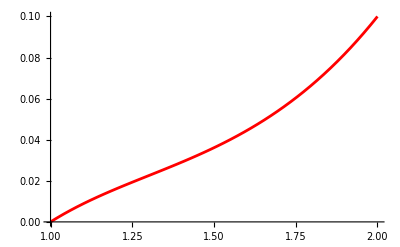

```mathematica
plotzex=Plot[Evaluate[z[r]/. s],{r,Rmin,Rmax},PlotRange->All, PlotStyle->Red]
```

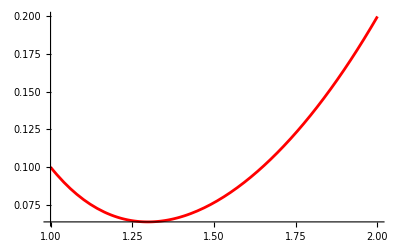

```mathematica
plotωex=Plot[Evaluate[z'[r]/. s],{r,Rmin,Rmax},PlotRange->All,PlotStyle->Red]
```

```mathematica
δ=1/100;
```

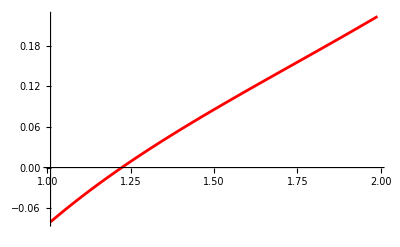

```mathematica
plotμex=Plot[Evaluate[H[r]/. s],{r,Rmin+δ,Rmax-δ},PlotStyle->Red]
```

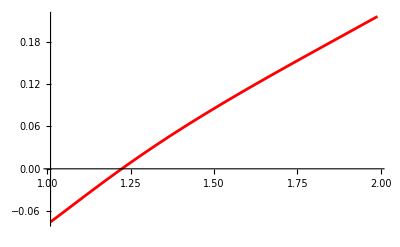

```mathematica
plotτex=Plot[Evaluate[1/sqrtdetg[r] ϕ'[r]/. s],{r,Rmin+δ,Rmax-δ},PlotRange->All,PlotStyle->{Red,Thickness->0.005}]
```

```mathematica
plotdFdlσ3dexact={ParametricPlot3D[{r Cos[θ],r Sin[θ],dFdlσ3d[r,θ][[1]]/.s[[1]]},{r,Rmin,Rmax},{θ,0,2π},PlotStyle->{Opacity[0.1]},AxesLabel->{"x","y","z"},BoxRatios->{1,1,1}],
ParametricPlot3D[{r Cos[θ],r Sin[θ],dFdlσ3d[r,θ][[2]]/.s[[1]]},{r,Rmin,Rmax},{θ,0,2π},PlotStyle->{Opacity[0.1]},AxesLabel->{"x","y","z"},BoxRatios->{1,1,1}],
ParametricPlot3D[{r Cos[θ],r Sin[θ],dFdlσ3d[r,θ][[3]]/.s[[1]]},{r,Rmin,Rmax},{θ,0,2π},PlotStyle->{Opacity[0.1]},AxesLabel->{"x","y","z"},BoxRatios->{1,1,1}]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
plotdFdlκ3dexact={ParametricPlot3D[{r Cos[θ],r Sin[θ],dFdlκ3d[r,θ][[1]]/.s[[1]]},{r,Rmin,Rmax},{θ,0,2π},PlotStyle->{Opacity[0.1]},AxesLabel->{"x","y","z"},BoxRatios->{1,1,1}],
ParametricPlot3D[{r Cos[θ],r Sin[θ],dFdlκ3d[r,θ][[2]]/.s[[1]]},{r,Rmin,Rmax},{θ,0,2π},PlotStyle->{Opacity[0.1]},AxesLabel->{"x","y","z"},BoxRatios->{1,1,1}],
ParametricPlot3D[{r Cos[θ],r Sin[θ],dFdlκ3d[r,θ][[3]]/.s[[1]]},{r,Rmin,Rmax},{θ,0,2π},PlotStyle->{Opacity[0.1]},AxesLabel->{"x","y","z"},BoxRatios->{1,1,1}]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
plotdFdlσκ3dexact={ParametricPlot3D[{r Cos[θ],r Sin[θ],dFdlσκ3d[r,θ][[1]]/.s[[1]]},{r,Rmin,Rmax},{θ,0,2π},PlotStyle->{Opacity[0.1]},AxesLabel->{"x","y","z"},BoxRatios->{1,1,1}],
ParametricPlot3D[{r Cos[θ],r Sin[θ],dFdlσκ3d[r,θ][[2]]/.s[[1]]},{r,Rmin,Rmax},{θ,0,2π},PlotStyle->{Opacity[0.1]},AxesLabel->{"x","y","z"},BoxRatios->{1,1,1}],
ParametricPlot3D[{r Cos[θ],r Sin[θ],dFdlσκ3d[r,θ][[3]]/.s[[1]]},{r,Rmin,Rmax},{θ,0,2π},PlotStyle->{Opacity[0.1]},AxesLabel->{"x","y","z"},BoxRatios->{1,1,1}]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
(*total force exerted on ds_r*)
```

```mathematica
Table[NIntegrate[N[dFdlσκ3d[Rmin,θ][[i]]/.s[[1]]] Rmin ,{θ,0,2π}],{i,1,3}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {0.417145}. NIntegrate obtained 1.48319×10^-15 and 4.68075×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {6.2831611214131084832670761514128443536719714757055044174194335938}. NIntegrate obtained 3.64726×10^-16 and 1.29393×10^-15 for the integral and error estimates.

{1.48319×10^-15,3.64726×10^-16,4.65491}

```mathematica
(*write z[r] vs r to file*)
```

```mathematica
tabzr=Table[{z[r]/.s[[1]],r},{r,Rmin,Rmax,(Rmax-Rmin)/100}]//N;
PrependTo[tabzr,{"f",":0"}]
Export["/Users/michelecastellana/Documents/finite_elements/steady-state-no-flow/solution-ode/z_r.csv",tabzr]
```

/Users/michelecastellana/Documents/finite_elements/steady-state-no-flow/solution-ode/z_r.csv

```mathematica
(*check z*)
```

```mathematica
znum=Import["~/Documents/finite_elements/steady_state/no_flow/solution/z.csv"];
znum=Table[{Sqrt[znum[[i,2]]^2+znum[[i,3]]^2],znum[[i,1]]},{i,2,Length[znum]}]
```

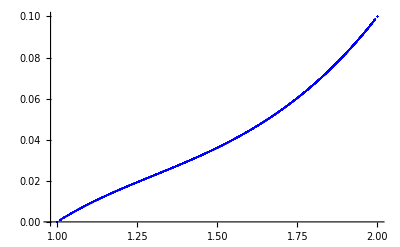

```mathematica
plotnum=ListPlot[znum,PlotRange->Full,PlotStyle->{Blue,Opacity->0.1}]
```

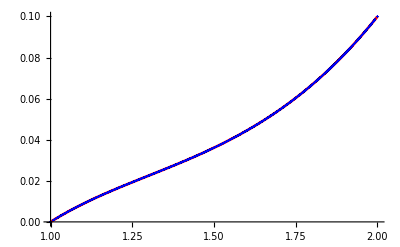

```mathematica
Show[plotzex,plotnum]
```

```mathematica
(*check ω*)
```

```mathematica
ω=Import["~/Documents/finite_elements/steady_state/no_flow/solution/omega.csv"];
ω=Table[{Sqrt[ω[[i,4]]^2+ω[[i,5]]^2],ω[[i,4]]/Sqrt[ω[[i,4]]^2+ω[[i,5]]^2] ω[[i,1]]+ω[[i,5]]/Sqrt[ω[[i,4]]^2+ω[[i,5]]^2] ω[[i,2]]},{i,2,Length[ω]}]
```

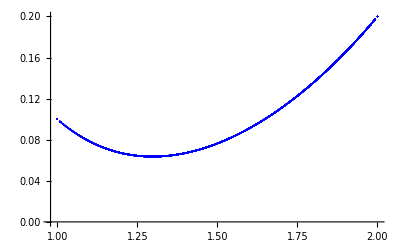

```mathematica
plotωnum=ListPlot[ω,PlotStyle->{Blue,Opacity->0.1}]
```

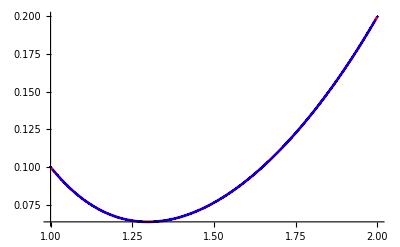

```mathematica
Show[plotωex,plotωnum]
```

```mathematica
(*check μ*)
```

```mathematica
μnum=Import["~/Documents/finite_elements/steady_state/no_flow/solution/mu.csv"];
μnum=Table[{Sqrt[μnum[[i,2]]^2+μnum[[i,3]]^2],μnum[[i,1]]},{i,2,Length[μnum]}]
```

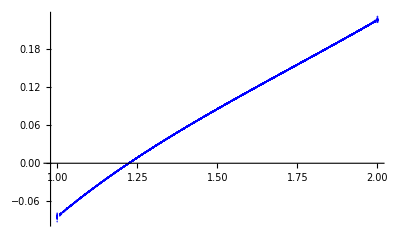

```mathematica
plotμnum=ListPlot[μnum,PlotStyle->{Blue,Opacity->0.1}]
```

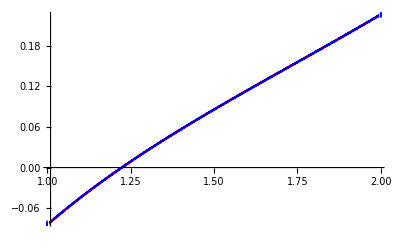

```mathematica
Show[plotμex,plotμnum]
```

```mathematica
(*check τ*)
```

```mathematica
τnum=Import["~/Documents/finite_elements/steady_state/no_flow/solution/tau.csv"];
τnum=Table[{Sqrt[τnum[[i,2]]^2+τnum[[i,3]]^2],τnum[[i,1]]},{i,2,Length[τnum]}]
```

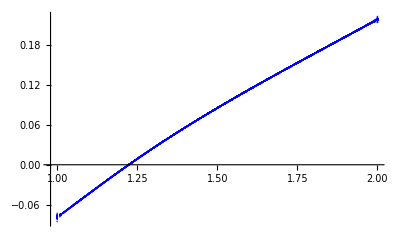

```mathematica
plotτnum=ListPlot[τnum,PlotStyle->{Blue,Opacity->0.1}]
```

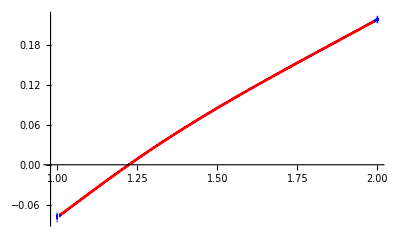

```mathematica
Show[plotτnum,plotτex]
```

```mathematica
(*test forces per unit length in 3d space*)
```

```mathematica
(*check tabdFdlσ3d*)
tabdFdlσ3d=Import["~/Documents/finite_elements/steady_state/no_flow/solution/nodal_values/dFdl_sigma_3d.csv"];
tabdFdlσ3d={Table[{tabdFdlσ3d[[i,4]],tabdFdlσ3d[[i,5]],tabdFdlσ3d[[i,1]]},{i,2,Length[tabdFdlσ3d]}],
Table[{tabdFdlσ3d[[i,4]],tabdFdlσ3d[[i,5]],tabdFdlσ3d[[i,2]]},{i,2,Length[tabdFdlσ3d]}],
Table[{tabdFdlσ3d[[i,4]],tabdFdlσ3d[[i,5]],tabdFdlσ3d[[i,3]]},{i,2,Length[tabdFdlσ3d]}]};
plottabdFdlσ3dfe={
ListPointPlot3D[tabdFdlσ3d[[1]],PlotRange->Full,PlotStyle->{PointSize->.01,Black,Opacity[.5]},AxesLabel->{"x","y","z"}],
ListPointPlot3D[tabdFdlσ3d[[2]],PlotRange->Full,PlotStyle->{PointSize->.01,Black,Opacity[.5]},AxesLabel->{"x","y","z"}],
ListPointPlot3D[tabdFdlσ3d[[3]],PlotRange->Full,PlotStyle->{PointSize->.01,Black,Opacity[.5]},AxesLabel->{"x","y","z"}]}
Show[plotdFdlσ3dexact[[1]],plottabdFdlσ3dfe[[1]]]
Show[plotdFdlσ3dexact[[2]],plottabdFdlσ3dfe[[2]]]
Show[plotdFdlσ3dexact[[3]],plottabdFdlσ3dfe[[3]]]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
(*check tabdFdlκ3d*)
tabdFdlκ3d=Import["~/Documents/finite_elements/steady_state/no_flow/solution/nodal_values/dFdl_kappa_3d.csv"];
tabdFdlκ3d={Table[{tabdFdlκ3d[[i,4]],tabdFdlκ3d[[i,5]],tabdFdlκ3d[[i,1]]},{i,2,Length[tabdFdlκ3d]}],
Table[{tabdFdlκ3d[[i,4]],tabdFdlκ3d[[i,5]],tabdFdlκ3d[[i,2]]},{i,2,Length[tabdFdlκ3d]}],
Table[{tabdFdlκ3d[[i,4]],tabdFdlκ3d[[i,5]],tabdFdlκ3d[[i,3]]},{i,2,Length[tabdFdlκ3d]}]};
plottabdFdlκ3dfe={
ListPointPlot3D[tabdFdlκ3d[[1]],PlotRange->Full,PlotStyle->{PointSize->.01,Black,Opacity[.5]},AxesLabel->{"x","y","z"}],
ListPointPlot3D[tabdFdlκ3d[[2]],PlotRange->Full,PlotStyle->{PointSize->.01,Black,Opacity[0.5]},AxesLabel->{"x","y","z"}],
ListPointPlot3D[tabdFdlκ3d[[3]],PlotRange->Full,PlotStyle->{PointSize->.01,Black,Opacity[0.5]},AxesLabel->{"x","y","z"}]}
Show[plotdFdlκ3dexact[[1]],plottabdFdlκ3dfe[[1]]]
Show[plotdFdlκ3dexact[[2]],plottabdFdlκ3dfe[[2]]]
Show[plotdFdlκ3dexact[[3]],plottabdFdlκ3dfe[[3]]]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
(*check tabdFdlσκ3d*)
tabdFdlσκ3d=Import["~/Documents/finite_elements/steady_state/no_flow/solution/nodal_values/dFdl_sigma_kappa_3d.csv"];
tabdFdlσκ3d={Table[{tabdFdlσκ3d[[i,4]],tabdFdlσκ3d[[i,5]],tabdFdlσκ3d[[i,1]]},{i,2,Length[tabdFdlσκ3d]}],
Table[{tabdFdlσκ3d[[i,4]],tabdFdlσκ3d[[i,5]],tabdFdlσκ3d[[i,2]]},{i,2,Length[tabdFdlσκ3d]}],
Table[{tabdFdlσκ3d[[i,4]],tabdFdlσκ3d[[i,5]],tabdFdlσκ3d[[i,3]]},{i,2,Length[tabdFdlσκ3d]}]};
plottabdFdlσκ3dfe={
ListPointPlot3D[tabdFdlσκ3d[[1]],PlotRange->Full,PlotStyle->{PointSize->.01,Black,Opacity[.5]},AxesLabel->{"x","y","z"}],
ListPointPlot3D[tabdFdlσκ3d[[2]],PlotRange->Full,PlotStyle->{PointSize->.01,Black,Opacity[.5]},AxesLabel->{"x","y","z"}],
ListPointPlot3D[tabdFdlσκ3d[[3]],PlotRange->Full,PlotStyle->{PointSize->.01,Black,Opacity[.5]},AxesLabel->{"x","y","z"}]}
Show[plotdFdlσκ3dexact[[1]],plottabdFdlσκ3dfe[[1]]]
Show[plotdFdlσκ3dexact[[2]],plottabdFdlσκ3dfe[[2]]]
Show[plotdFdlσκ3dexact[[3]],plottabdFdlσκ3dfe[[3]]]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
tabve=Import["/Users/michelecastellana/Documents/finite_elements/steady-state-no-flow/mesh/solution/vertices.csv"]
tabve=Drop[tabve,{1}]
ListPlot[tabve,PlotStyle->Blue,AspectRatio->1]
```

Import::nffil: File /Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/mesh/solution/vertices.csv not found during Import.

$Failed

Drop::drop: Cannot drop positions 1 through 1 in $Failed.

Drop[$Failed,{1}]

Drop::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Drop[False,True].

ListPlot::lpn: Drop[$Failed,{1}] is not a list of numbers or pairs of numbers.

ListPlot[Drop[$Failed,{1}],PlotStyle→RGBColor[0, 0, 1],AspectRatio→1]

```mathematica
(*write z from ODE to csv file*)
```

```mathematica
tabz=Table[{z[r]/.s[[1]]/.{r->Norm[tabve[[i]]]},tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabz,{"f",":0",":1",":2"}]
```

Part::partd: Part specification Drop[$Failed,{1}]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification Drop[$Failed,{1}]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of {1} does not exist.

{{f,:0,:1,:2},{InterpolatingFunction[…][Norm[$Failed]],Drop[$Failed,{1}]⟦1,1⟧,Drop[$Failed,{1}]⟦1,2⟧,0},{-1.62025688270356×10^-15,1,Drop[$Failed,{1}]⟦2,2⟧,0}}

```mathematica
Export["/Users/michelecastellana/Documents/finite_elements/steady-state-no-flow/solution-ode/z_ode.csv",tabz]
```

/Users/michelecastellana/Documents/finite_elements/steady-state-no-flow/solution-ode/z_ode.csv

```mathematica
(*write omega=z' from ODE to csv file*)
```

```mathematica
tabω=Table[{z'[r]/.s[[1]]/.{r->Norm[tabve[[i]]]},tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabω,{"f",":0",":1",":2"}]
```

Part::partd: Part specification Drop[$Failed,{1}]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification Drop[$Failed,{1}]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of {1} does not exist.

{{f,:0,:1,:2},{InterpolatingFunction[…][Norm[$Failed]],Drop[$Failed,{1}]⟦1,1⟧,Drop[$Failed,{1}]⟦1,2⟧,0},{0.10000000000000761423331264,1,Drop[$Failed,{1}]⟦2,2⟧,0}}

```mathematica
Export["/Users/michelecastellana/Documents/finite_elements/steady-state-no-flow/solution-ode/omega_ode.csv",tabω]
```

/Users/michelecastellana/Documents/finite_elements/steady-state-no-flow/solution-ode/omega_ode.csv

```mathematica
(*write mu=H from ODE to csv file*)
```

```mathematica
tabμ=Table[{H[r]/.s[[1]]/.{r->Norm[tabve[[i]]]},tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabμ,{"f",":0",":1",":2"}]
```

Part::partd: Part specification Drop[$Failed,{1}]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification Drop[$Failed,{1}]⟦1,2⟧ is longer than depth of object.

Part::partw: Part 2 of {1} does not exist.

{{f,:0,:1,:2},{(InterpolatingFunction[…][Norm[$Failed]]+(InterpolatingFunction[…][Norm[$Failed]])^3+Norm[$Failed] InterpolatingFunction[…][Norm[$Failed]])/(2 Norm[$Failed] (1+(InterpolatingFunction[…][Norm[$Failed]])^2)^(3/2)),Drop[$Failed,{1}]⟦1,1⟧,Drop[$Failed,{1}]⟦1,2⟧,0},{-0.08437980049221333277039,1,Drop[$Failed,{1}]⟦2,2⟧,0}}

```mathematica
Export["/Users/michelecastellana/Documents/finite_elements/steady-state-no-flow/solution-ode/mu_ode.csv",tabμ]
```

/Users/michelecastellana/Documents/finite_elements/steady-state-no-flow/solution-ode/mu_ode.csv